Jai Prasadh
PHY 315 HW10
Based on program by Daniel Heinzen

```mathematica
(*Program "incoherent michelson.nb." This simulates the output of a Michelson interferometer illuminated with incoherent light.psi1(t) and psi2(t) are the fields of the two output waves at a specific point on a screen or a detector.We simulate an incoherent wave for psi1(t) by superposing nmax waves,each with a random frequency omega[n] in the range from omegamin to omegamax,random amplitude A[n] between 0 and 1,and a random phase phi[n] between 0 and 2 Pi.psi2(t) is the same function,except that it is time delayed by 2 deltaL/v,where deltaL is the difference between the lengths L1 and L2 of the inteferometer arms,and v is the wave velocity.We set deltaL=alpha lambda,where lambda is the wavelength for the average wave frequency omegeav.The resultant output wave is psi(t)=psi1(t)+psi2(t).The output intensity is I(t)=psi(t)^2. Ibar is the time average of I(t) over the period 0 to tmax.*)
```

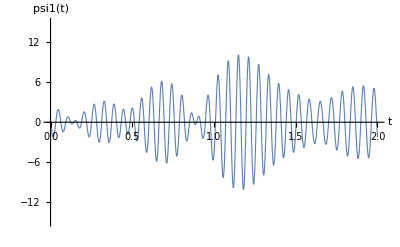

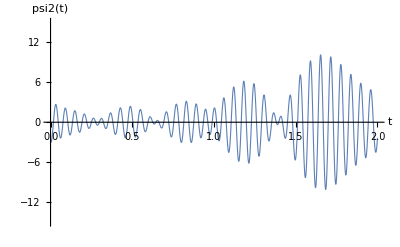

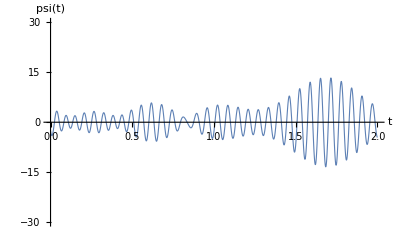

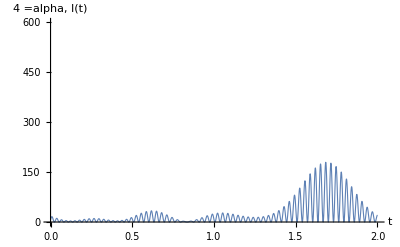

DeltaL/lambda | Ibar
4 | 19.0271

```mathematica
alpha:=4;(*Sets your deltaL in units of lambda.Change this number to change your deltaL*)tmax:=4;(*This is the integration time for the calculation of the time-averaged intensity Ibar.A longer tmax is better,but if tmax is too large it may cause the integration to fail*)nmax:=100;(*The number of waves superposed to make the incoherent input wave*)omegamin:=90;(*The lowest frequency contained in the input wave*)omegamax:=110;(*The highest frequency contained in the input wave*)omegaav:=(omegamax+omegamin)/2 (*The average frequency in the input wave*)

v:=50;(*The velocity of the wave*)lambda:=(2 Pi v)/omegaav;(*The wavelength for the average frequency*)deltaL:=alpha lambda;(*The difference in the length of the two interferometer arms*)(*The next 3 lines define 3 vectors A,omega,and phi,containing the nmax random amplitudes,frequencies,and phases of the underlying components waves of the incoherent wave psi1(t)*)A=RandomReal[{0,1},nmax];
omega=RandomReal[{omegamin,omegamax},nmax];
phi=RandomReal[{0,2 Pi},nmax];

(*The next two lines define the two output waves psi1(t) and psi2(t).psi2(t) is time delayed by the propagation time difference 2 deltaL/v between the two interferometer arms.*)
psi1[t_]:=Sum[A[[n]] Cos[omega[[n]] t+phi[[n]]],{n,1,nmax}]
psi2[t_]:=Sum[A[[n]] Cos[omega[[n]] (t-2 deltaL/v)+phi[[n]]],{n,1,nmax}]
psi[t_]=psi1[t]+psi2[t];(*The resultant wave*)Intensity[t_]:=psi[t]^2;(*The intensity of the resultant wave*)(*The next four lines make plots of psi1(t),psi2(t),psi(t),and I(t)*)Plot[psi1[t],{t,0,2},PlotRange->{-1.5 Sqrt[nmax],1.5 Sqrt[nmax]},AxesLabel->{"t","psi1(t)"},PlotStyle->Thickness[0.002],AxesStyle->Directive[Thickness[0.002],FontSize->14]]
Plot[psi2[t],{t,0,2},PlotRange->{-1.5 Sqrt[nmax],1.5 Sqrt[nmax]},AxesLabel->{"t","psi2(t)"},PlotStyle->Thickness[0.002],AxesStyle->Directive[Thickness[0.002],FontSize->14]]
Plot[psi[t],{t,0,2},PlotRange->{-3 Sqrt[nmax],3 Sqrt[nmax]},AxesLabel->{"t","psi(t)"},PlotStyle->Thickness[0.002],AxesStyle->Directive[Thickness[0.002],FontSize->14]]
Plot[Intensity[t],{t,0,2},PlotRange->{0,6 nmax},AxesLabel->{"t","=alpha, I(t)"alpha},PlotStyle->Thickness[0.002],AxesStyle->Directive[Thickness[0.002],FontSize->14]]

(*The next four lines calculate the time averaged intensity Ibar,and make a table showing deltaL and Ibar for that deltaL*)
Ibar:=NIntegrate[Intensity[t],{t,0,tmax}]/tmax
column1={"DeltaL/lambda",alpha};
column2={"Ibar",Ibar};
Coefftable=Transpose[Join[{column1},{column2}]];
Grid[Coefftable,Frame->All,ItemStyle->Directive[FontSize->14]]
```

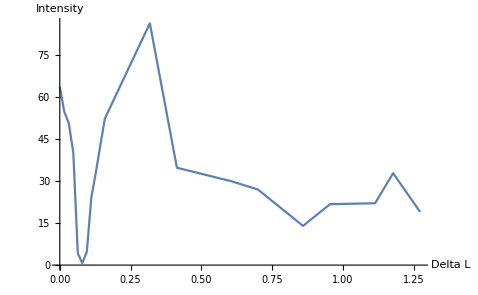

```mathematica
data={{0,63.7996},{0.015915494,54.8806},{0.031830989,50.7499},{0.047746483,40.233},{0.063661977,4.19824},{0.079577472,0.708418},{0.095492966,4.75527},{0.11140846,24.1446},{0.127323954,33.1286},{0.143239449,42.7854},{0.159154943,52.3971},{0.318309886,86.5293},{0.413802852,34.841},{0.604788784,30.0468},{0.70028175,27.0361},{0.859436693,14.0291},{0.954929659,21.7975},{1.114084602,22.1258},{1.177746579,32.8836},{1.273239545,19.0271}};
Show[ListPlot[data,Joined->True],AxesLabel->{"Delta L","Intensity"}]
```